# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Rayleigh Scattering

General form:

```mathematica
pRayleigh[u_,γ_]:=1/(4 Pi)3/(4(1+2γ))((1+3γ)+(1-γ)u^2)
```

Common special case (γ = 0):

```mathematica
pRayleigh[u_]:=(1+u^2)3/(16 Pi)
```

### Normalization condition

```mathematica
Integrate[2 Pi pRayleigh[u],{u,-1,1}]
```

1

```mathematica
Integrate[2 Pi pRayleigh[u,y],{u,-1,1},Assumptions->y>0]//Simplify
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi pRayleigh[u]u,{u,-1,1}]
```

0

```mathematica
Integrate[2 Pi pRayleigh[u,y] u,{u,-1,1},Assumptions->y>0]//Simplify
```

0

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

0

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi}]
```

1/2

### sampling

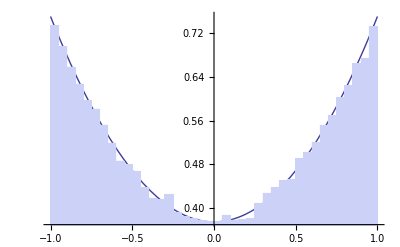

```mathematica
Show[
Plot[2 Pi pRayleigh[u],{u,-1,1}],
Histogram[Map[(1-(2-4 #+√(5+16 (-1+#)#))^(2/3))/(2-4 #+√(5+16 (-1+#) #))^(1/3)&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
Clear[b];
```